```mathematica
Integrate[Log[x]/x^(1/2),{x,0,n}]
```

2 √n (-2+Log[n])

```mathematica
FullSimplify[Integrate[Log[x]^k/x^(1/2),{x,1,n}],Element[k,Integers]]
```

ConditionalExpression[(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2]),k≥0&&Log[n]>0]

```mathematica
intlog[n_,k_]:=(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2])
sumlog[n_,k_]:=Sum[Log[x]^k/x^(1/2),{x,1,n}]
dlog[n_,k_]:=sumlog[n,k]-intlog[n,k]
dlog2[n_,k_]:=sumlog[n,k]-(-ExpIntegralE[-k,-Log[n]/2] Log[n]^(1+k))
```

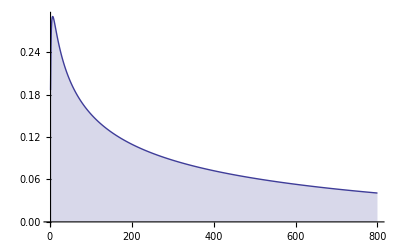

```mathematica
DiscretePlot[{Re@dlog[n,1]},{n,2,800}]
```

```mathematica
FullSimplify[Integrate[Log[x]^k/x^(1/2),{x,1,n}],Element[k,Integers]]
```

ConditionalExpression[(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2]),k≥0&&Log[n]>0]

```mathematica
Chop@dlog[1000000,4.]
```

18.218

```mathematica
sumlog[n,1]
```

-1/4 (2 EulerGamma+π+Log[64]+2 Log[π]) Zeta[1/2]+Zeta^(1,0)[1/2,1+n]

```mathematica
Chop@dlog[1800000,2.]
```

-15.931+1.0374×10^-10 ⅈ

```mathematica
dlog[n,1]
```

4 (-1+Gamma[2,-Log[n]/2])-1/4 (2 EulerGamma+π+Log[64]+2 Log[π]) Zeta[1/2]+Zeta^(1,0)[1/2,1+n]

```mathematica
dlog[100000.,1.]
```

3.94085+7.36809×10^-13 ⅈ

```mathematica
dlog[1000000.,1.]
```

3.92955+2.89397×10^-12 ⅈ

```mathematica
Table[dlog[1000000.,k],{k,1,20}]
```

{3.92955+2.89397×10^-12 ⅈ,-15.9129+7.03468×10^-11 ⅈ,97.3218+1.30447×10^-9 ⅈ,-749.782+2.17774×10^-8 ⅈ,7931.66+3.44158×10^-7 ⅈ,-88683.3+6.13983×10^-6 ⅈ,1.33827×10^6+0.0000899973 ⅈ,-1.99802×10^7+0.00130568 ⅈ,3.80757×10^8+0.0187965 ⅈ,-7.30512×10^9+0.978346 ⅈ,1.65249×10^11+3.83083 ⅈ,-3.89981×10^12-66.936 ⅈ,1.02358×10^14+768.713 ⅈ,-2.85204×10^15+31816.5 ⅈ,8.57635×10^16+152640. ⅈ,-2.74151×10^18-1.51509×10^6 ⅈ,9.32535×10^19+3.00833×10^7 ⅈ,-3.35652×10^21+1.06486×10^9 ⅈ,1.27556×10^23+5.89641×10^9 ⅈ,-5.10213×10^24-3.1436×10^10 ⅈ}

```mathematica
N@20!
```

2.4329×10^18

```mathematica
dlog2[1000000.,11]/11!
```

4139.84+9.59704×10^-8 ⅈ

```mathematica
dlog2[100000.,11]/11!
```

4114.66+3.62024×10^-9 ⅈ

```mathematica
Chop@Table[dlog2[10000.,k]/k!,{k,1,20}]//TableForm
```

3.9687
-7.7921
16.6516
-30.5007
66.7616
-123.761
261.578
-505.578
1030.57+1.03684×10^-10 ⅈ
-2041.95+3.56646×10^-10 ⅈ
4101.07
-8188.11
16386.8
-32766.2
65537.1
-131071.
262144.
-524288.
1.04858×10^6
-2.09715×10^6

```mathematica
Chop@Table[dlog2[100000.,k]/k!,{k,1,20}]//TableForm
```

3.94085
-7.89939
16.4027
-30.8424+1.27754×10^-10 ⅈ
66.6651+4.00106×10^-10 ⅈ
-122.886+8.19979×10^-10 ⅈ
264.411+1.42186×10^-9 ⅈ
-499.896+2.13721×10^-9 ⅈ
1039.48+2.83552×10^-9 ⅈ
-2030.17+1.22486×10^-8 ⅈ
4114.66+3.62024×10^-9 ⅈ
-8174.1-4.37862×10^-9 ⅈ
16399.9+3.21408×10^-9 ⅈ
-32755.+7.89763×10^-9 ⅈ
65546.+2.09994×10^-9 ⅈ
-131065.-1.08327×10^-9 ⅈ
262149.+1.05227×10^-9 ⅈ
-524285.+1.72127×10^-9 ⅈ
1.04858×10^6+4.17326×10^-10 ⅈ
-2.09715×10^6

```mathematica
Chop@Table[dlog2[1000000.,k]/k!,{k,1,20}]//TableForm
```

3.92955
-7.95646
16.2203+2.17412×10^-10 ⅈ
-31.2409+9.07393×10^-10 ⅈ
66.0971+2.86798×10^-9 ⅈ
-123.171+8.52754×10^-9 ⅈ
265.53+1.78566×10^-8 ⅈ
-495.542+3.23828×10^-8 ⅈ
1049.26+5.17981×10^-8 ⅈ
-2013.1+2.69606×10^-7 ⅈ
4139.84+9.59704×10^-8 ⅈ
-8141.53-1.39741×10^-7 ⅈ
16437.6+1.23448×10^-7 ⅈ
-32715.1+3.64958×10^-7 ⅈ
65584.7+1.16726×10^-7 ⅈ
-131030.-7.24136×10^-8 ⅈ
262178.+8.45779×10^-8 ⅈ
-524262.+1.66323×10^-7 ⅈ
1.0486×10^6+4.84722×10^-8 ⅈ
-2.09714×10^6-1.29212×10^-8 ⅈ

```mathematica
Chop@Table[(-1)^(k+1) 2^(k+1),{k,1,20}]//TableForm
```

4
-8
16
-32
64
-128
256
-512
1024
-2048
4096
-8192
16384
-32768
65536
-131072
262144
-524288
1048576
-2097152

```mathematica
zv[k_]:=(-1)^(k+1) 2^(k+1)
```

```mathematica
zz := {3.929553892847673,-7.956461430038549,16.220296829406422,  -31.24091502455548,66.09712576771827,-123.17120161528628,265.5303322565017,-495.5416983733711,1049.2644258860655,-2013.0959043772134,4139.8379919593535,-8141.529649237544,16437.63643590042,-32715.070374004863,65584.74998887476,-131029.90587445711,262178.20893203217,-524261.74367646256,1.0485950918186842*^6,-2.097138811838005*^6}
zs[z_,n_]:=Zeta[1/2]+Sum[z^k zv[k],{k,0,n}]
zs2[z_,n_]:=Zeta[1/2]+Sum[z^k zz[[k]],{k,1,n}]
```

```mathematica
zs2[0.1,20]
```

-1.13331

```mathematica
Zeta[.6]
```

-1.95266

```mathematica
zz[[6]]
```

-123.171

```mathematica
zv[6]
```

-128

```mathematica
sl[n_,k_]:=(Sum[Log[x]^k/x^(1/2),{x,1,n}]-Integrate[Log[x]^k/x^(1/2),{x,0,n}])k!
```

```mathematica
N[sl[100000,2]]
```

-31.5976

```mathematica
N[-2 √n (-2+Log[n])-1/4 (2 EulerGamma+π+Log[64]+2 Log[π]) Zeta[1/2]+Derivative[1,0][Zeta][1/2,1+n]/.n->10000000000000000]
```

3.92265-8.53367×10^-7 ⅈ

```mathematica
Table[(N@Im@ZetaZero@1 I)^k,{k,0,10}]
```

{1.+0. ⅈ,0.+14.1347 ⅈ,-199.79+0. ⅈ,0.-2823.98 ⅈ,39916.2+0. ⅈ,0.+564205. ⅈ,-7.97488×10^6+0. ⅈ,0.-1.12723×10^8 ⅈ,1.59331×10^9+0. ⅈ,0.+2.25209×10^10 ⅈ,-3.18327×10^11+0. ⅈ}

```mathematica
Cz1[n_,s_]:=Sum[Cos[s Log[j]]/j^(1/2),{j,1,n}]-Integrate[Cos[s Log[j]]/j^(1/2),{j,0,n}]
Cz2[n_,s_]:=Sum[(1+Sum[(-1)^k (s Log[j])^(2k)/((2k)!),{k,1,Infinity}])/j^(1/2),{j,1,n}]-Integrate[(1+Sum[(-1)^k (s Log[j])^(2k)/((2k)!),{k,1,Infinity}])/j^(1/2),{j,0,n}]
Cz3[n_,s_]:=(Sum[(1)/j^(1/2),{j,1,n}]-Integrate[(1)/j^(1/2),{j,0,n}])+Sum[(Sum[(-1)^k (s Log[j])^(2k)/((2k)!),{k,1,Infinity}])/j^(1/2),{j,1,n}]-Integrate[(Sum[(-1)^k (s Log[j])^(2k)/((2k)!),{k,1,Infinity}])/j^(1/2),{j,0,n}]
Cz4[n_,s_]:=(-2 √n+HarmonicNumber[n,1/2])+Sum[(Sum[(-1)^k (s Log[j])^(2k)/((2k)!),{k,1,Infinity}])/j^(1/2),{j,1,n}]-Integrate[(Sum[(-1)^k (s Log[j])^(2k)/((2k)!),{k,1,Infinity}])/j^(1/2),{j,0,n}]
Cz5[n_,s_]:=(-2 √n+HarmonicNumber[n,1/2])+Sum[Sum[((-1)^k (s Log[j])^(2k)/((2k)!))/j^(1/2),{j,1,n}]-Integrate[((-1)^k (s Log[j])^(2k)/((2k)!))/j^(1/2),{j,0,n}],{k,1,Infinity}]
Cz6[n_,s_]:=(-2 √n+HarmonicNumber[n,1/2])+Sum[s^(2k)(Sum[((-1)^k ( Log[j])^(2k)/((2k)!))/j^(1/2),{j,1,n}]-Integrate[((-1)^k ( Log[j])^(2k)/((2k)!))/j^(1/2),{j,0,n}]),{k,1,Infinity}]
Cz7[n_,s_]:=(-2 √n+HarmonicNumber[n,1/2])+Sum[(-1)^k s^(2k)/((2k)!)(Sum[(( Log[j])^(2k))/j^(1/2),{j,1,n}]-Integrate[( ( Log[j])^(2k))/j^(1/2),{j,0,n}]),{k,1,Infinity}]
Cz8[n_,s_]:=(-2 √n+HarmonicNumber[n,1/2])+Sum[(-1)^k s^(2k)/((2k)!)(Sum[(( Log[j])^(2k))/j^(1/2),{j,1,n}]-(2^(1+2 k) Gamma[1+2 k,-Log[n]/2])),{k,1,Infinity}]
Cz9[n_,s_]:=Zeta[1/2]+Sum[(-1)^k s^(2k)/((2k)!)zv[2k],{k,1,Infinity}]
Cz9a[n_,s_]:=Zeta[1/2]+Sum[s^k/(k!)zv[k],{k,1,Infinity}]
Ex7[n_,s_]:=(-2 √n+HarmonicNumber[n,1/2])+Sum[ s^k/(k!)(Sum[(( Log[j])^k)/j^(1/2),{j,1,n}]-Integrate[( ( Log[j])^k)/j^(1/2),{j,0,n}]),{k,1,Infinity}]
Ex7a[n_,s_]:=(-2 √n+HarmonicNumber[n,1/2])+Sum[ s^k/(k!)(Sum[(( Log[j])^k)/j^(1/2),{j,1,n}]-(-ExpIntegralE[-k,-Log[n]/2] Log[n]^(1+k))),{k,1,Infinity}]

Ez1[n_,s_]:=Sum[Cos[s Log[j]]/j^(1/2),{j,1,n}]-Integrate[Cos[s Log[j]]/j^(1/2),{j,0,n}] + I(Sum[Sin[s Log[j]]/j^(1/2),{j,1,n}]-Integrate[Sin[s Log[j]]/j^(1/2),{j,0,n}])
```

```mathematica
N@Ex7[100,1/10I + 1/10]
```

-1.01878+0.297658 ⅈ

```mathematica
N@Cz9a[10000,(240/10)+(1/10)I]
```

0.539645+5.55112×10^-17 ⅈ

```mathematica
Zeta[.6+.1I]
```

-1.80556-0.580585 ⅈ

```mathematica
N@Ez1[100,.1I + .1]
```

-1.77841+0.590908 ⅈ

```mathematica
Cz1[100,.4+.1I]
```

-0.67567+0.216651 ⅈ

```mathematica
(Zeta[.5+(.4+.1I)I]+Zeta[.5-(.4+.1I)I])/2
```

-0.661649+0.240722 ⅈ

```mathematica
Sum[(-1)^k (s Log[j])^(2k)/((2k)!),{k,0,Infinity}]
```

Cos[s Log[j]]

```mathematica
(Sum[(1)/j^(1/2),{j,1,n}]-Integrate[(1)/j^(1/2),{j,0,n}])
```

-2 √n+HarmonicNumber[n,1/2]

```mathematica
N[dlog2[1000000,2]/dlog2[1000000,1]]
```

-4.04955+2.08843×10^-11 ⅈ

```mathematica
N[dlog2[100000,2]/dlog2[100000,1]]
```

-4.00898+4.46399×10^-12 ⅈ

```mathematica
FullSimplify[Integrate[(  Log[j])^(2k)/j^(1/2),{j,0,n}],Element[k,Integers]]
```

ConditionalExpression[2^(1+2 k) Gamma[1+2 k,-Log[n]/2],k>-1/2]

```mathematica
2^(1+2 k) Gamma[1+2 k,-Log[n]/2]
```

$Aborted

```mathematica
FullSimplify[Integrate[Log[j]^k/j^(1/2),{j,0,n}],Element[k,Integers]]
```

ConditionalExpression[(-1)^k 2^(1+k) Gamma[1+k,-Log[n]/2],k>-1]

```mathematica
-ExpIntegralE[-k,-Log[n]/2] Log[n]^(1+k)
```

```mathematica
(-1)^k 2^(1+k) Gamma[1+k,-Log[n]/2]/.k->3/.n->100.
```

658.862-3.69776×10^-13 ⅈ

```mathematica
-ExpIntegralE[-k,-Log[n]/2] Log[n]^(1+k)/.k->3/.n->100.
```

658.862-3.69776×10^-13 ⅈ

```mathematica
Integrate[Log[x]^3/x^(1/2),{x,1,n}]
```

ConditionalExpression[96+2 √n (-48+24 Log[n]-6 Log[n]^2+Log[n]^3),Re[n]≥0||n∉Reals]

```mathematica
CForm[2 √n (-48+Log[n] (24+(-6+Log[n]) Log[n]))]
```

2*Sqrt(n)*(-48 + Log(n)*(24 + (-6 + Log(n))*Log(n)))

```mathematica
CForm[96+2 √n (-48+24 Log[n]-6 Log[n]^2+Log[n]^3)]
```

96 + 2*Sqrt(n)*(-48 + 24*Log(n) - 6*Power(Log(n),2) + Power(Log(n),3))

```mathematica
FullSimplify[Integrate[Log[x]^k/x^(1/2),{x,0,n}],Element[k,Integers]]
```

ConditionalExpression[(-1)^k 2^(1+k) Gamma[1+k,-Log[n]/2],k>-1]

```mathematica
FullSimplify[Integrate[Log[x]^k/x^(1/2),{x,1,n}],Element[k,Integers]]
```

ConditionalExpression[(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2]),k≥0&&Log[n]>0]

```mathematica
intlog[n_,k_]:=(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2])
sumlog[n_,k_]:=Sum[Log[x]^k/x^(1/2),{x,2,n}]
dlog[n_,k_]:=sumlog[n,k]-intlog[n,k]
edlog[n_,z_,l_]:=Sum[z^k/k! dlog[n,k],{k,0,l}]
```

```mathematica
edlog[1000,N@Im@ZetaZero@1, 100]
```

5.5165×10^131+4.16913×10^28 ⅈ

```mathematica
Zeta[.5-.4]
```

-0.603038

```mathematica
edlog[100,z]
```

$Aborted

```mathematica
gah[1.1]
```

1.21248×10^69+1.16953×10^-9 ⅈ

```mathematica
Zeta[.5-.3]
```

-0.733921

```mathematica
Integrate[ Cos[s Log[j]]/j^(1/2),{j,0,1}]
```

ConditionalExpression[2/(1+4 s^2),s∈Reals]

```mathematica
Integrate[ Sin[s Log[j]]/j^(1/2),{j,0,1}]
```

ConditionalExpression[-(4 s)/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
Integrate[j^(I s)/j^(1/2),{j,0,1}]
```

ConditionalExpression[(2 ⅈ)/(ⅈ-2 s),Im[s]<1/2]

```mathematica
FullSimplify[2/(1+4 s^2)+I(-(4 s)/(1+4 s^2))]
```

(2 ⅈ)/(ⅈ-2 s)

```mathematica
Integrate[ Cos[s Log[j]]/j^(1/2),{j,0,n}]
```

∫_0^n Cos[s Log[j]]/(√j)ⅆj

```mathematica
Integrate[ Cos[s Log[j]]/j^(1/2),{j,1,n}]
```

ConditionalExpression[(-2+2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2),Re[n]≥0||n∉Reals]

```mathematica
pos[n_,s_]:=1+Sum[Cos[s Log[j]]/j^(1/2),{j,2,n}]-((-2+2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2)+2/(1+4 s^2))
pos2[n_,s_]:=Sum[Cos[s Log[j]]/j^(1/2),{j,1,n}]-((-2+2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2)+2/(1+4 s^2))
```

```mathematica
pos[100,10.]
```

1.52027

```mathematica
(Zeta[.5+10I]+Zeta[.5-10I])/2
```

1.5449+0. ⅈ

```mathematica
FullSimplify[Integrate[ Cos[s Log[j]]/j^(1/2),{j,1,n}]+Integrate[ Cos[s Log[j]]/j^(1/2),{j,0,1}]]
```

ConditionalExpression[(2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2),s∈Reals&&(Re[n]≥0||n∉Reals)]